# Continued Fraction Square Packing

Adam Rumpf, 5/23/2018

## Introduction

There is a geometric interpretation of continued fractions where, to represent a number q, we begin with a 1×q rectangle and try filling it from left to right with 1×1 squares (this represents “skimming off” the integer part of q). This may leave some space on the right, resulting in a skinnier 1×(q-⌊q⌋) rectangle. Then fill it from top to bottom with (q-⌊q⌋)×(q-⌊q⌋) rectangles (this represents “skimming off” the integer part of 1/(q-⌊q⌋)). This may leave some space underneath. The process continues on like this. If q is irrational, the process never ends, so we have to just pick a finite number of layers to draw.

We can program this as an iterative process, where in each itration we begin by knowing the coordinates of the top left corner, whether we are moving right or down, and the amount of vertical or horizontal space to fill. If we ever end up with zero space left over, we terminate early. Rather than always moving down and to the right, we can continue to rotate clockwise to end up with a spiral similar to the golden spiral.

The main function defined below is called boxes[]. It accepts two arguments: a number q to approximate, and a number of iterations n to conduct. The output is a graphic of packed boxes corresponding to the continued fraction representation of q, truncated after n iterations. All boxes generated within the same iteration are the same size and color, which begins red and shifts towards violet in later iterations. Any empty space left due to truncation error is gray.

## Code

### Initialization

```mathematica
(* unit vectors *)
dir[0]={1,0};
dir[1]={0,-1};
dir[2]={-1,0};
dir[3]={0,1};
```

```mathematica
(* given a starting coordinate, a direction, and nonzero fill dimensions, generates a list of Rectangle objects filling in the given space with unit boxes, and also outputs the new starting point, leftover dimensions, and direciton *)
boxgen[start_,d_,dim_]:=Module[{rec,size,num,end,newdim,ϵ=0.001},
size=Min[dim];(* box size *)
If[size>0,
(* nondegenerate *)
num=Quotient[Max[dim],size];(* number of boxes *)
rec=Table[Rectangle[start+size i dir[d],start+size i dir[d]+size(dir[d]+dir[Mod[d-1,4]])],{i,0,num-1}];
end=start+size (num-1) dir[d]+size(dir[d]+dir[Mod[d-1,4]]);(* last coordinate *)
newdim={Mod[Max[dim],size],size},(* leftover space *)
(* degenerate *)
rec={Rectangle[start,start]};
end=start;
newdim={0,0};
];
If[newdim[[1]]<ϵ,
newdim[[1]]=0;(* zero out dimension if it's small enough *)
];
{rec,end,newdim,Mod[d+1,4]}
]
```

```mathematica
(* given a list of rectangle objects and a color vector, displays the assembled figure *)
showboxes[g_,c_]:=Graphics[Join[{EdgeForm[Thick]},Riffle[c,g]]]
```

```mathematica
(* generates the box colors, starting with a background color and then generating one color for each box *)
colgen[n_]:=Join[{Gray},Table[Hue[i],{i,0,0.9,0.9/(n-1)}]]
```

```mathematica
(* given a starting number and a desired number of terms, generates the graphics object of the corresponding box spiral, terminating early if too many terms are specified *)
boxes[q_,n_]:=Module[{boxes={{Rectangle[{0,0},{q,1}]}},colors=colgen[n],start={0,0},d=0,dim={q,1},temp},
Do[
temp=boxgen[start,d,dim];
boxes=Append[boxes,temp[[1]]];
start=temp[[2]];
dim=temp[[3]];
d=temp[[4]],
{i,1,n}];
showboxes[boxes,colors]
]
```

### Demonstration

We can start with the example of 2.75, which has a finite continued fraction representation [2;1,3] since 2.75=2+1/(1+1/3). In the picture below we can see these boxes forming a clockwise spiral: 2 red, 1 cyan, and 3 magenta.

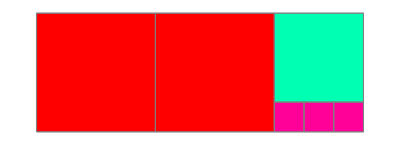

```mathematica
boxes[2.75,3]
```

Next we can try √2, which has an infinite continued fraction representation [1;2,2,2,...], or √2=1+1/(2+1/(2+1/(2+...))). In the picture below we can see these digits appear from the 1 red box, followed by 2, each, of the green, blue, and magenta boxes. The leftover gray space is left due to truncation error.

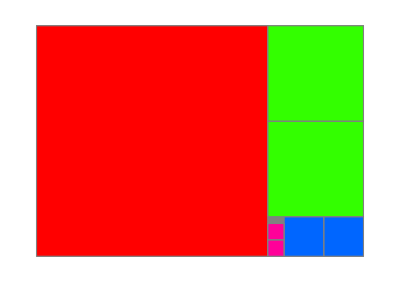

```mathematica
boxes[√2,4]
```

Taking more terms fills in some of this blank area, and also shifts the rest of the colors since the color selection function defined above chooses colors with hues evenly distributed on [0,1].

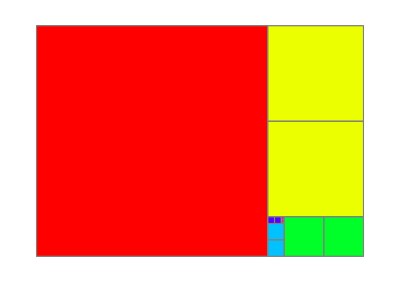

```mathematica
boxes[√2,6]
```

The golden spiral is generated by the golden ratio ϕ=(1+√5)/2, which has an infinite representation [1;1,1,1,...] or ϕ=1+1/(1+1/(1+1/(1+...))). This is shown in the picture below by the fact that there is exactly one box of each color and size.

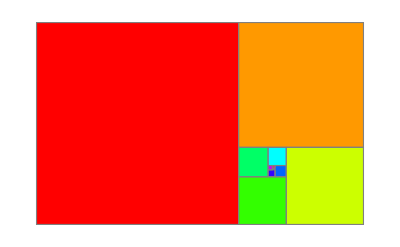

```mathematica
boxes[GoldenRatio,10]
```

Here is a Manipulate that allows the user to select a number between 1 and 2.

```mathematica
Manipulate[boxes[q,10],{{q,√2},1,2}]
```